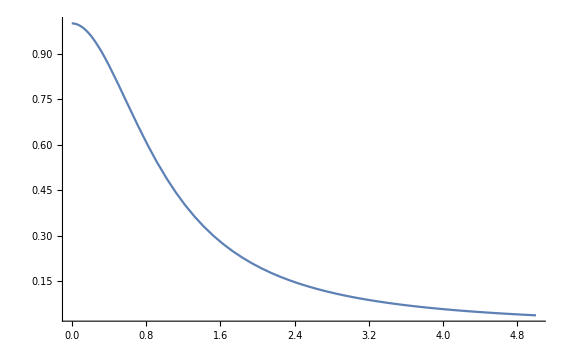

```mathematica
Plot[1/(1+x^2),{x,0,5},PlotRange->Full]
```

Idée principale

Approximer cos α ≈ e^(-x^2/2)

```mathematica
Series[Cos[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

```mathematica
Series[Exp[-x^2/2],{x,0,10}]
```

1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+O[x]^11

```mathematica
Manipulate[Plot[{Cos[x]^s,Exp[-s x^2/2]},{x,0,π/2},PlotRange->{0,1}],{{s,4},0,64}]
```

Convolution de 2 gaussiennes : σ_0^2+σ_1^2=σ_2^2